# Q5

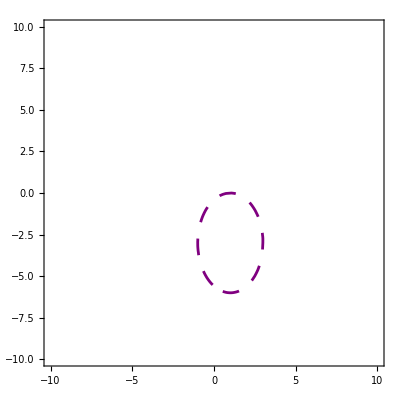

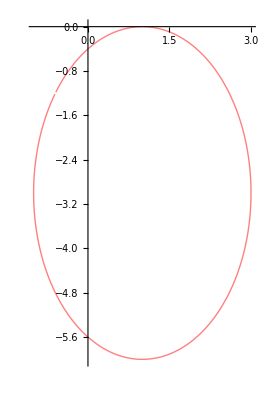

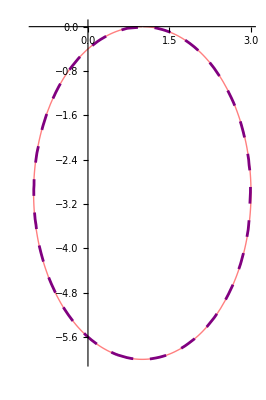

A

```mathematica
f[x_,y_]:=9 x^2+4 y^2-18x+24y+9
(*i*)
g1=ContourPlot[
f[x,y]==0,
{x,-10,10},
{y,-10,10},
ContourStyle->{Purple,Dashing[0.03]}
]
f[r*Cos[t],r*Sin[t]];
s=Solve[f[r*Cos[t],r*Sin[t]]==0,{r}];
g2=PolarPlot[
s[[1,1,2]],
{t,0,2*Pi},
PlotStyle->{Pink,Thick}
]
Show[g2,g1]
(*ii*)
Style[Text["A"],100]
```